# Drawing Robot

## PACKAGE LOADING (please ignore)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Directory[];
```

```mathematica
PrependTo[$Path , NotebookDirectory[] ];
```

```mathematica
<<ScrewCalculusPro`;
```

```mathematica
?HomogeneousRotX
```

```mathematica
?ScrewCalculusPro`*
```

## POSITION TRAJECTORY (please ignore)

```mathematica
Tanc[t_] = Tan[t]^(1/Tan[t]);
cuoredx[t_] = {Tanc[t] Cos[t] , Tanc[t] Sin[t], 0 };(*t from 0 to Pi/2-0.01*)
cuoresx[t_] =  {-Tanc[t] Cos[t] , Tanc[t] Sin[t] , 0};
off1 = Pi/2 - 0.05;
a = cuoredx[off1];
b = cuoresx[off1];
c = {3, -1, 2.7};
```

```mathematica
h = RotZ[Pi].c;
```

```mathematica
off2 = Pi/2 + 0.05;
```

```mathematica
k = 3off2;
scarto=0.2;
```

```mathematica
Manipulate[ParametricPlot3D[cuoredx[(t+0.03)/3], {t, 0, s}, PlotRange->2], {s, 0.01,3off1 }];
```

```mathematica
cuorecentro[t_] = (t-3off1)/0.2*b + (1-(t-3off1)/0.2)*a;
```

```mathematica
cuorecentro[3off1];
```

```mathematica
cuorecentro[3off1+0.2];
```

```mathematica
Manipulate[ParametricPlot3D[cuorecentro[t], {t, 3off1, s}, PlotRange->1], {s, 3off1+0.01,3off1+0.2}];
```

```mathematica
const = 3off1+0.2;
```

```mathematica
off3 = const+3 off1-0.7;
cuoresx[t_] =  {-Tanc[off1-(t-const)/3] Cos[off1-(t-const)/3], Tanc[off1-(t-const)/3] Sin[off1-(t-const)/3], 0};
```

```mathematica
Manipulate[ParametricPlot3D[cuoresx[t], {t, const, s}, PlotRange->2], {s, const+0.02,off3}];
```

```mathematica
cuoresx[off2+0.01];
```

```mathematica
cuore[t_] = Piecewise[{{RotX[2Pi/5].cuoredx[(t+0.1)/3]+h,3 off1≥t≥0}, {RotX[2Pi/5].cuorecentro[t]+h, const≥t≥3off1}, {RotX[2Pi/5].cuoresx[t]+h, off3≥t≥const}}];
```

```mathematica
cuoresx[const+3off1-0.7];
```

```mathematica
Manipulate[ParametricPlot3D[cuore[t], {t, 0, s}, PlotRange->8, AxesLabel->{i, j, "k"}], {s, 0.011, off3}];
```

paintbrush

```mathematica
a = RotZ[Pi].{2, 1, 1};
b = RotZ[Pi].{2, 1, 0.2};
tcarica=0.5;
carica[t_] =2 t*b + (1-2t)*a;
scarica[t_] = 2(t-tcarica)*a + (1-2(t-tcarica))*b;
carica1[t_] =2 (t-2*tcarica)*b + (1-2(t-2*tcarica))*a;
scarica1[t_] = 2(t-3*tcarica)*a + (1-2(t-3*tcarica))*b;
car[t_] = {a[[1]], a[[2]],0.6+0.4*Sin[t*(2 Pi)+Pi/2]};
avvio[t_] = {Sin[(t-2)*Pi/4]+2, 2Cos[(t-2)*Pi/4]-1,1+ (t-2)*3/4} ;
pennello[t_]=Piecewise[{{car[t], 0≤t≤2}, {RotZ[Pi].avvio[t] , 4≥t≥2}}];
Manipulate[ParametricPlot3D[pennello[t], {t, 0, s}, PlotRange->{{0,-4},{0,-4}, {0,4}}, AxesLabel->{x,y,"z"}], {s, 0.01, 4}];
```

comeback

```mathematica
tfc = 4+off3;
z = cuore[off3];
```

```mathematica
h;
```

```mathematica
riposo[t_] = (1-0.5(t - tfc))*z + 0.5(t-tfc)*a;
```

ensemble

```mathematica
tf = tfc + 2;
```

```mathematica
path[t_] = Piecewise[{{pennello[t], 4≥t≥0}, {cuore[t-4], tfc≥t≥4}, {riposo[t], tf≥t≥tfc}}];
```

```mathematica
Manipulate[ParametricPlot3D[path[t], {t, 0, s}, PlotRange->8, AxesLabel->{i, j, "k"}], {s, 0.01,tf}];
```

```mathematica
v[t_] = D[path[t],t];
```

```mathematica
vcarica[t_] = D[car[t],t];
```

```mathematica
vavvio[t_] = D[avvio[t],t];
```

```mathematica
vcuoredx[t_]=D[cuoredx[t],t];
```

```mathematica
vcuorecentro[t_] = D[cuorecentro[t],t] ;
```

```mathematica
vcuoresx[t_] = D[cuoresx[t],t];
```

```mathematica
vritorno = D[riposo[t], t];
```

```mathematica
(*v[t_] = Piecewise[{ {vcarica[t], 0≤t≤2}, {vavvio[t], 2≤t≤4}, {vcuoredx[t], 4≤t≤4+3off1}, {vcuorecentro[t], 4+3off1≤t≤4+const},{vcuoresx[t], 4+const≤t≤tfc}, {riposo[t], tfc≤t≤tf}  }];*)
```

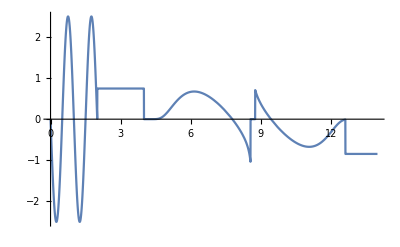

```mathematica
Plot[v[t][[3]], {t,0,14}, PlotRange->All]
```

## ANGULAR TRAJECTORY (please ignore)

```mathematica
RotZYX[{a_,b_,c_}]:=RotZ[a].RotY[b].RotX[c]
```

```mathematica
config0 = {0,-Pi/2,0};
config1 = {0,-Pi,0};
config2 = {0,-Pi/2,-Pi/2+Pi/4};
e = RollPitchYawAngles[RotZYX[config0]];
f = RollPitchYawAngles[RotZYX[config1]];
g = RollPitchYawAngles[RotZYX[config2]];
conf1 = RollPitchYawMatrix[f];
conf2 = RollPitchYawMatrix[g];
anglecarica[t_] := RollPitchYawMatrix[(1-10t)*e + 10t*f];(*t da 0 a 0.1*)
angleavvio[t_] :=RollPitchYawMatrix[(1-0.5(t-2))*f +0.5(t-2)*g];
anglepath[t_] := Piecewise[{{anglecarica[t], 0≤t≤0.1}, {conf1, 0.1≤t≤2}, {angleavvio[t], 2≤t≤4}, {conf2, 4≤t≤tf}}];
```

```mathematica
xdes[t_] =  Piecewise[{{anglecarica[t].{1,0,0}, 0≤t≤0.1}, {conf1.{1,0,0}, 0.1≤t≤2}, {angleavvio[t].{1,0,0}, 2≤t≤4}, {conf2.{1,0,0}, 4≤t≤tf}}];
ydes[t_] =  Piecewise[{{anglecarica[t].{0,1,0}, 0≤t≤0.1}, {conf1.{0,1,0}, 0.1≤t≤2}, {angleavvio[t].{0,1,0}, 2≤t≤4}, {conf2.{0,1,0}, 4≤t≤tf}}];
zdes[t_] = Piecewise[{{anglecarica[t].{0,0,1}, 0≤t≤0.1}, {conf1.{0,0,1}, 0.1≤t≤2}, {angleavvio[t].{0,0,1}, 2≤t≤4}, {conf2.{0,0,1}, 4≤t≤tf}}];
```

```mathematica
desframe=Manipulate[Show[Graphics3D[{{Blue,Line[{path[t],path[t]+xdes[t]}]},{Green,Line[{path[t],path[t]+ydes[t]}]},{Magenta,Line[{path[t],path[t]+zdes[t]}]}}],PlotRange->5,AxesLabel->{x,y,z},ImageSize->700],{t,0,0.12}];
```

```mathematica
wcarica[t_]:=SkewToAxis[D[anglecarica[t],t].Transpose[anglecarica[t]]];
wavvio[t_] := SkewToAxis[D[angleavvio[t],t].Transpose[angleavvio[t]]];
```

```mathematica
ω[t_] = Piecewise[{{wcarica[t], 0.1≥t≥0}, {{0,0,0}, 2≥t≥0.1}, {wavvio[t], 4≥t≥2}, {{0,0,0}, tf≥t≥4}}];
```

Screws::wrongDimension: -- Message text not found --

## GEOMETRIC DESIGN (please ignore)

Arms

```mathematica
l0 = 3;
l1 = 2.5;
l2 = 1.8;
l3 = 0.3;
```

Initial Configuration

```mathematica
q1i = 0.3;
q2i = 0.2;
q3i = 0.2;
q4i = 0.8;
q5i = -Pi/4;
q6i = 0.6;
qo = {q1i, q2i, q3i, q4i, q5i, q6i};
```

## ROBOT KINEMATICS (please ignore)

Denavit-Hartenberg

```mathematica
Ta1[q1_] = DH[{0,Pi/2,l0,q1,"R"}];
T12[q2_] = DH[{l1,0,0,q2+Pi/2,"R"}];
T23[q3_] = DH[{0,-Pi/2,0,q3,"R"}];
T34[q4_] = DH[{0,Pi/2,l2,q4,"R"}];
T45[q5_] = DH[{0,-Pi/2,0,q5,"R"}];
T5EE[q6_] = DH[{0,0,l3,q6,"R"}];
```

```mathematica
TaEE[q1_,q2_,q3_,q4_,q5_,q6_]=Ta1[q1].T12[q2].T23[q3].T34[q4].T45[q5].T5EE[q6];
```

```mathematica
poseff[q1_,q2_,q3_,q4_,q5_,q6_]=RigidPosition[TaEE[q1,q2,q3,q4,q5,q6]];
orienteff[q1_,q2_,q3_,q4_,q5_,q6_] = RigidOrientation[TaEE[q1,q2,q3,q4,q5,q6]];
```

```mathematica
xdesee[{q1_,q2_,q3_,q4_,q5_,q6_}]=orienteff[q1,q2,q3,q4,q5,q6].{1,0,0};
ydesee[{q1_,q2_,q3_,q4_,q5_,q6_}]=orienteff[q1,q2,q3,q4,q5,q6].{0,1,0};
zdesee[{q1_,q2_,q3_,q4_,q5_,q6_}]=orienteff[q1,q2,q3,q4,q5,q6].{0,0,1};
prova = {0,0,0,0,0,0};
Show[Graphics3D[{{Blue,Line[{path[0],path[0]+xdesee[prova]}]},{Green,Line[{path[0],path[0]+ydesee[prova]}]},{Magenta,Line[{path[0],path[0]+zdesee[prova]}]}}],PlotRange->5,AxesLabel->{x,y,z},ImageSize->700];
```

Jacobian

```mathematica
jacobiano[{q1_,q2_,q3_,q4_,q5_,q6_}] = DHJacob0[{{0,Pi/2,l0,q1,"R"},{l1,0,0,q2+Pi/2,"R"},{0,-Pi/2,0,q3,"R"},{0,Pi/2,l2,q4,"R"},{0,-Pi/2,0,q5,"R"},{0,0,l3,q6,"R"}}];
```

```mathematica
Det[jacobiano[{0.4,0.1, 2,3, 0.5,1}]] // MatrixForm
```

-0.591776

```mathematica
Inverse[jacobiano[qo]]
```

{{0.137159,-0.443397,2.91266×10^-18,-0.0237302,-0.00734061,-0.117396},{-0.359128,-0.111091,-0.158935,0.0052799,0.0647732,-0.057205},{0.466715,0.144372,-0.39662,0.0357394,0.0886986,0.0743423},{0.0642503,-0.481073,0.398531,-0.462632,-0.994994,-1.16447},{-0.165581,0.269779,0.387059,-0.0738831,-0.850218,0.726356},{-0.0153273,0.436152,-0.563608,-0.603208,1.01815,1.03144}}

Kinematic Controller

```mathematica
TEEa[q1_,q2_,q3_,q4_,q5_,q6_]=Inverse[TaEE[q1,q2,q3,q4,q5,q6]];
```

```mathematica
REEa[q1_,q2_,q3_,q4_,q5_,q6_]=  RigidOrientation[TEEa[q1,q2,q3,q4,q5,q6]];
```

```mathematica
eP[t_,{q1_,q2_,q3_,q4_,q5_,q6_}] := path[t] - poseff[q1,q2,q3,q4,q5,q6];
(*eO[t_,{q1_,q2_,q3_,q4_,q5_,q6_}] := RollPitchYawAngles[anglepath[t]]-RollPitchYawAngles[orienteff[q1,q2,q3,q4,q5,q6]];*)
eO[t_,{q1_,q2_,q3_,q4_,q5_,q6_}] := QuatVectPart[anglepath[t].REEa[q1,q2,q3,q4,q5,q6]]
```

```mathematica
KP = 20Eye[3];
KO = 5 Eye[3];
```

```mathematica
qdot[t_?NumericQ,{q1_?NumericQ,q2_?NumericQ,q3_?NumericQ,q4_?NumericQ,q5_?NumericQ,q6_?NumericQ}]:=
Inverse[jacobiano[{q1,q2,q3,q4,q5,q6}]].(Join[v[t]+KP.eP[t,{q1,q2,q3,q4,q5,q6}], ω[t]+KO.eO[t,{q1,q2,q3,q4,q5,q6}] ])
```

Kinematic Integration

```mathematica
tstart=0.01;
```

```mathematica
tend = tf-0.1;
```

```mathematica
sol=NDSolve[Join[{Equal[D[q[t],t],qdot[t,q[t]]],Equal[q[tstart],qo]}],q[t],{t,tstart,tend}]
```

{{q[t]→InterpolatingFunction[…][t]}}

```mathematica
sol = sol[[1]];
```

```mathematica
qsol[t_]=Evaluate[q[t]/.sol];
```

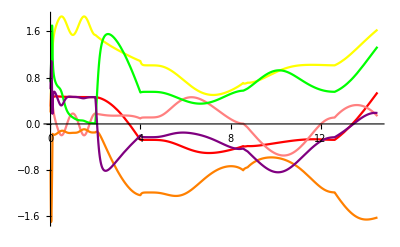

```mathematica
Plot[{qsol[t][[1]],qsol[t][[2]],qsol[t][[3]],qsol[t][[4]],qsol[t][[5]], qsol[t][[6]]},{t,tstart,tend},PlotStyle->{Red,Yellow,Pink,Green,Orange, Purple}]
```

```mathematica
ePsol[t_]=eP[t,qsol[t]];
eOsol[t_] = eO[t,qsol[t]];
```

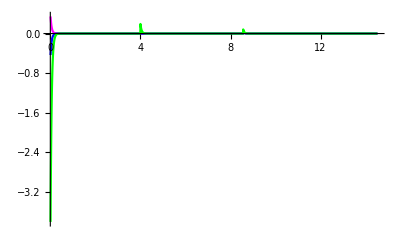

```mathematica
Plot[{ePsol[t][[1]], ePsol[t][[2]], ePsol[t][[3]]},{t,tstart,tend},PlotStyle->{Magenta, Blue, Green},PlotRange->All]
```

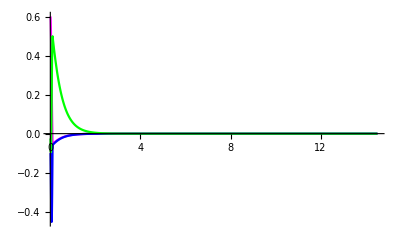

```mathematica
Plot[{eOsol[t][[1]], eOsol[t][[2]], eOsol[t][[3]]},{t,tstart,tend},PlotStyle->{Magenta, Blue, Green},PlotRange->All]
```

## ROBOT CONSTRUCTION (please ignore)

```mathematica
raggioarm = 0.2
```

0.2

```mathematica
link1[q1_]:=Graphics3D[{Green,Opacity[0.5],Specularity[White,20],Cylinder[{{0,0,0},RigidPosition[Ta1[q1]]},raggioarm]}]
link2[q1_,q2_]:=Graphics3D[{Green,Opacity[0.5],Specularity[White,20],Cylinder[{RigidPosition[Ta1[q1]],RigidPosition[Ta1[q1].T12[q2]]},raggioarm-0.05]}];
link3[q1_,q2_,q3_,q4_]:=Graphics3D[{Green,Opacity[0.5],Specularity[White,20],Cylinder[{RigidPosition[Ta1[q1].T12[q2]],RigidPosition[Ta1[q1].T12[q2].T23[q3].T34[q4]]},raggioarm-0.1]}];
link6[q1_,q2_,q3_,q4_,q5_,q6_]:=Graphics3D[{Yellow,Opacity[0.5],Specularity[White,20],Cylinder[{RigidPosition[Ta1[q1].T12[q2].T23[q3].T34[q4].T45[q5]],RigidPosition[Ta1[q1].T12[q2].T23[q3].T34[q4].T45[q5].T5EE[q6]]},raggioarm-0.15]}];
```

```mathematica
robot[q1_,q2_,q3_,q4_,q5_,q6_]={link1[q1], link2[q1,q2], link3[q1,q2,q3,q4], link6[q1,q2,q3,q4,q5,q6]};
```

```mathematica
Show[robot[0,0,0,0,0,0]]
```

-Graphics3D-

## PLANET (please ignore)

```mathematica
h;
```

```mathematica
arr = h - {0,0,0.7};
raggioeasel = 0.1;
```

```mathematica
secch =  RotZ[Pi].{2, 1, 0};
```

```mathematica
planepts=Table[{x,y,0},{x,-15,15,5},{y,-10,30,5}];
plane=Map[Graphics3D,{Map[{Gray,Line[#]}&,planepts],Map[{Gray,Line[#]}&,Transpose[planepts]]}];
easel = Graphics3D[{Brown, Opacity[0.5],Specularity[Orange,20], Cylinder[{{-4,0.7,0},arr},raggioeasel],  Cylinder[{{-2,0.7,0},arr},raggioeasel], Cylinder[{{-3,1.3,0},arr},raggioeasel]}];
canvas = Graphics3D[{Glow[White], Opacity[1], Parallelepiped[arr-{1,0,0},{{2,0,0},RotX[-Pi/10].{0,0.2,0},RotX[-Pi/10].{0,0,3}}]}];
bucket1 =  Cylinder[{secch, secch+{0,0,0.6}},0.4] ;
bucket2 =  Cylinder[{secch, secch+{0,0,0.6}},0.45] ;
bucket =DiscretizeRegion[RegionDifference[bucket2,bucket1]];
filling = Graphics3D[{Glow[Yellow],Opacity[1],  Cylinder[{secch, secch+{0,0,0.5}}, 0.4]}];
floor = Graphics3D[{Lighter[Green], Opacity[0.5],Specularity[Black,100],  Parallelepiped[{5,20,-0.01},{{-40,0,0},{0,-30,0},{0,0,0.009}}]}];
```

## MOVIE (please ignore)

```mathematica
geometry[{q1_,q2_,q3_,q4_,q5_,q6_}]= {plane, easel, canvas, bucket, filling,floor, robot[q1,q2,q3,q4,q5,q6]};
prova={0,Pi/2,0,0,0,0};
Show[geometry[prova], Boxed->False, Background->Lighter[LightCyan], PlotRange->{{-7,2},{10,-4},{-0.1,7}}, ImageSize-> 500];
```

```mathematica
heart[t_] = Piecewise[{{cuore[t-4], 4≤t≤tfc}}];
```

```mathematica
paint:=Animate[Show[geometry[{qsol[t][[1]], qsol[t][[2]], qsol[t][[3]], qsol[t][[4]], qsol[t][[5]], qsol[t][[6]]}], ParametricPlot3D[heart[s], {s, 4, t}, PlotStyle->Directive[{Blue, Thickness[0.008]}]], Boxed->False, Background->Lighter[LightCyan], PlotRange->{{-7,2},{8,-4},{-0.1,6}}, ImageSize-> 600, ViewPoint->{-1, -2.4, 2.}], {t,tstart,tend}, AnimationRepetitions->1, AnimationRate->0.7 ]
```

## PLAY

```mathematica
paint
```